# On Device Control

## Assignment -5

PH1050

Aarya Gosar (EP23B025)

Engineering Physics

20th Sept 2023

## Problem Statement

Our Goal is to create a surveillance system by using our webcam from Mathematica.
		 It must Identify the intruder and play an alarm to notify the owners.

## My approach

As this assignment was open ended, I decided to take a unique approach. 
	-First, I take My image and store it as innocent person
	-I compare the faces which appear in real time with my face
	-If it is very different from my original image, it classifies that person as an intrude

## Aim

1) Store my image locally
2) In a loop, Compare all the faces that appear in real time
3) Highlight the faces that are not me
4) Play an alarm when it spots an intruder
5) Plot the errors for faces and see the difference between my error and intruder’s error

## Code

```mathematica
Clear["Global`*"]
img = CurrentImage[];
face = FindFaces[img][[1]];
grayface = ColorConvert[img,"Grayscale"];
cropface =ImageResize[ImageTake[grayface,face[[1]],face[[2]]],{75,130}]
Export["Face.jpg",cropface];
DeviceClose["Camera"]
(* Store the Grayscale version of my face {Mathematica stores it upside down}*)
```

-Graphics-

```mathematica
MyFace = Import["Face.jpg"];

(* Creating beats *)
signal=Play[Sin[340 2 Pi  t] + Sin[345 2 Pi  t],{t,0,2}];

(*storing errors to plot it later*)
errors = {};

dev = DeviceOpen["Camera"];
Dynamic[img]

For[i = 0,i<10,i ++,

 img = CurrentImage[]; 
faces = FindFaces[img];

(* Iterating over all the faces *) 
For[j=1, j<=Length[faces],j++,
greyimg = ColorConvert[img,"Grayscale"];
Pause[0.1];
facePerson = ImageResize[ImageTake[greyimg,faces[[j]][[1]],faces[[j]][[2]]],{75,130}];
(* Take pixel wise difference of the face and my original face *);
error = Total[Flatten[ImageData[ImageDifference[MyFace,facePerson]]]];
If[error > 1000, EmitSound[signal];img = HighlightImage[img,faces[[j]]];, Print["Aarya"];];
AppendTo[errors,error]
];

]
DeviceClose[dev]
```

Note: The Program identifies Venkatakrishna as intruder, but not me

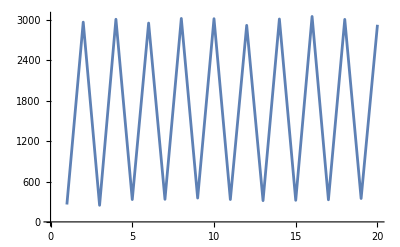

```mathematica
ListLinePlot[errors]
```

As we can see the graph oscillates between 2 values, 
The higher error is of Venkatakrishna who was sitting behind me
The lower error is mine

## Conclusion

We can see from plot, there is a clear difference in error of the two faces

I didn’t Like the idea of comparing two successive image as it doesnt differentiate me from intruder.